# Computational Analysis of the Time Dependent Schroedinger Equation

By: Andrew DeBenedictis, Anna Phillips, and Jen Radoff

## Introduction

## Importing Python-generated data

```mathematica
NotebookDirectory[]
```

/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 6/GradStudentsRock_TDSE/

```mathematica
path=NotebookDirectory[];
cases={"freeParticle","squareWell","harmonicOscillator","triangle","kronigPenney","imagPotential","complexPotential","barrier1","barrier2","barrier3"};
scheme={"_SFD","_CN"};
numberType={"Real","Imag"};
periodicType={"periodic","nonPeriodic"};
eigenState = {"eValues","eVectors"};
```

## Free Particle

Let’s look at the eigenvalues and eigenvectors to start out siCNe these are scheme-independent:

```mathematica
Clear[freeEVectorsRe,freeEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
freeEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["freeEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
freeEVectors=Sqrt[freeEVectorsRe^2+freeEVectorsIm^2];
];
```

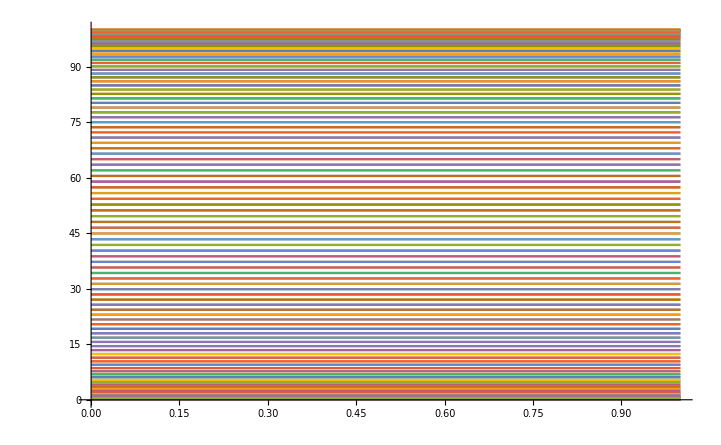

```mathematica
Plot[freeEValues,{x,0,1}]
```

```mathematica
Manipulate[ListPlot[freeEVectors⟦i,All⟧,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{i,1,Length[freeEVectors⟦All,1⟧],1}]
```

### Scheme 1: Simple Finite DiffereCNe (SFD)

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeRe,freeIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
Do[
Evaluate[Symbol["free"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
free=Sqrt[freeRe^2+freeIm^2];
];
```

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeRe⟦t,All⟧,freeIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeRe⟦All,1⟧],1}]
```

### Scheme 2: Crank-Nicolson (CN)

This should be the most stable scheme. For the rest of the cases, we will implement this scheme.

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeCNRe,freeCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeCN=Sqrt[freeCNRe^2+freeCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeCN⟦t,All⟧,freeCNRe⟦t,All⟧,freeCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

#### compare the two schemes directly

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeCN⟦t,All⟧},PlotRange->{0,.7},Joined->True,PlotLegends->{"Simple finite difference", "Crank-Nicolson"},DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

#### and check normalization

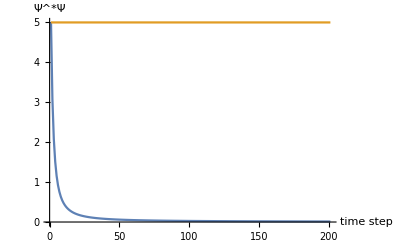

```mathematica
ListPlot[{Total[free^2,{2}],Total[freeCN^2,{2}]},Joined->True,AxesLabel->{"time step","Ψ^*Ψ"}]
```

Scheme 2 doesn’t lose normalization!

### Scheme 2 with non-Periodic boundary conditions

```mathematica
Clear[freeNonPeriodicCNRe,freeNonPeriodicCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeNonPeriodicCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeNonPeriodicCN=Sqrt[freeNonPeriodicCNRe^2+freeNonPeriodicCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeNonPeriodicCN⟦t,All⟧,freeNonPeriodicCNRe⟦t,All⟧,freeNonPeriodicCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeNonPeriodicCNRe⟦All,1⟧],1}]
```

PINBALL!!!!

## Square Well

With a wave packet.

```mathematica
Clear[squareCNRe,squareCNIm,squareCN,squarePotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=2;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["squareCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
squarePotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
squareCN=Sqrt[squareCNRe^2+squareCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareCN⟦t,All⟧,squareCNRe⟦t,All⟧,squareCNIm⟦t,All⟧,squarePotential},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,Joined->True],{t,1,Length[squareCNRe⟦All,1⟧],1}]
```

## Harmonic Oscillator

Non-periodic

```mathematica
Clear[hoCNRe,hoCNIm,hoCN,hoPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=3;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["hoCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
hoPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
hoCN=Sqrt[hoCNRe^2+hoCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoCN⟦t,All⟧,hoCNRe⟦t,All⟧,hoCNIm⟦t,All⟧,hoPotential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,DataRange->{-20,20}, AxesOrigin->{-20,0},Joined->True],{t,1,Length[hoCNRe⟦All,1⟧],1}]
```

## Triangle

Non-periodic

```mathematica
Clear[triCNRe,triCNIm,triCN,triPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=4;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["triCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
triPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
triCN=Sqrt[triCNRe^2+triCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{triCN⟦t,All⟧,triCNRe⟦t,All⟧,triCNIm⟦t,All⟧,triPotential},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[triCNRe⟦All,1⟧],1}]
```

## Kronig-Penney

Periodic

```mathematica
Clear[kpCNRe,kpCNIm,kpCN,kpPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=5;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["kpCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
kpPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
kpCN=Sqrt[kpCNRe^2+kpCNIm^2];
];
Manipulate[ListPlot[{kpCN⟦t,All⟧,kpCNRe⟦t,All⟧,kpCNIm⟦t,All⟧,kpPotential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[kpCNRe⟦All,1⟧],1}]
```

## Barrier

Non-periodic. Grid size is large compared to barrier width.

### Height = E

```mathematica
Clear[b1CNRe,b1CNIm,b1CN,b1Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=8;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b1CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b1Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b1CN=Sqrt[b1CNRe^2+b1CNIm^2];
];
Manipulate[ListPlot[{b1CN⟦t,All⟧,b1CNRe⟦t,All⟧,b1CNIm⟦t,All⟧,b1Potential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b1CNRe⟦All,1⟧],1}]
```

### Height < E

```mathematica
Clear[b2CNRe,b2CNIm,b2CN,b2Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=9;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b2CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b2Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b2CN=Sqrt[b2CNRe^2+b2CNIm^2];
];
Manipulate[ListPlot[{b2CN⟦t,All⟧,b2CNRe⟦t,All⟧,b2CNIm⟦t,All⟧,b2Potential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b2CNRe⟦All,1⟧],1}]
```

### Height > E

```mathematica
Clear[b3CNRe,b3CNIm,b3CN,b3Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=10;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b3CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b3Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b3CN=Sqrt[b3CNRe^2+b3CNIm^2];
];
Manipulate[ListPlot[{b3CN⟦t,All⟧,b3CNRe⟦t,All⟧,b3CNIm⟦t,All⟧,b3Potential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b3CNRe⟦All,1⟧],1}]
```

## V=ix

Non-periodic

```mathematica
Clear[imagCNRe,imagCNIm,imagCN,imagPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=6;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["imagCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
imagPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
imagCN=Sqrt[imagCNRe^2+imagCNIm^2];
];
Manipulate[ListPlot[{imagCN⟦t,All⟧,imagCNRe⟦t,All⟧,imagCNIm⟦t,All⟧,Im[imagPotential]},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

## V=x+ix

Non-periodic

```mathematica
Clear[complexCNRe,complexCNIm,complexCN,complexPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=7;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["complexCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
complexPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
complexCN=Sqrt[complexCNRe^2+complexCNIm^2];
];
Manipulate[ListPlot[{complexCN⟦t,All⟧,complexCNRe⟦t,All⟧,complexCNIm⟦t,All⟧,complexPotential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

## Discussion?

About the non-Hermitian-ness...